#### Function definitions

```mathematica
Clear["Global`*"]
s={15,FontFamily->"Times New Roman"};
```

```mathematica
k=8.617330 10^-5;(*eV/K*)
Δ=50 10^-6; (*eV*)
hbar=6.582119569×10^-16;(*eV s*)
ele=1.602176634×10^-19; (*elementary charge in C*)
α=hbar/(k 2ele 10^6);
Tc=0.47;(*K*)
linspace[start_,stop_,n_:100]:=N[Table[x,{x,start,stop,(stop-start)/(n-1)}]]

gap[T_] := 1-√(2 Pi k T/Δ)Exp[-Δ/(k T)](*temperature dependence of BCS gap (first order expansion at small T)*)
gap2[T_] := Tanh[1.74 Sqrt[Tc/T-1]](* alternatively, use this phenomenological temperature dependence*)


(*fitting function f=I(V) function according to Eq. (1). The input arguments are
Bias v in μV
Critical supercurrent in μA
R1,R2 in Ω
 T in K *)
f[v_, i0_, r1_, r2_, T_]:=N[i0 gap[T] Im[BesselI[1-I α v /((r1+r2) T),α i0 gap[T]/T]/BesselI[-I α v /((r1+r2) T),α i0 gap[T]/T]]]
(*version fitting function that takes array of voltages vList instead of single quantity*)
fpoints[vlist_, i0_?NumericQ,r1_?NumericQ,r2_?NumericQ, T_?NumericQ]:=N[Table[f[v,i0, r1,r2,T],{v, vlist}]]
vmax=5;
```

#### Load data sets for a selected number of temperatures.

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\2x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\4x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\6x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\8x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\10x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\12x.csv

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\processed_data\t_dependence\13x.csv

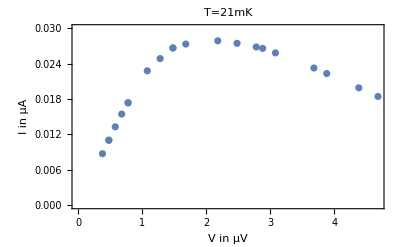
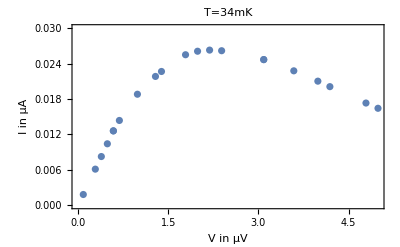
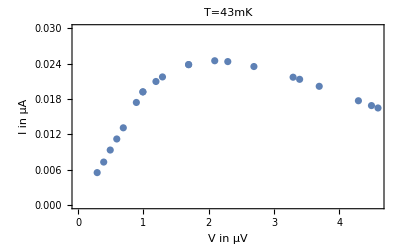
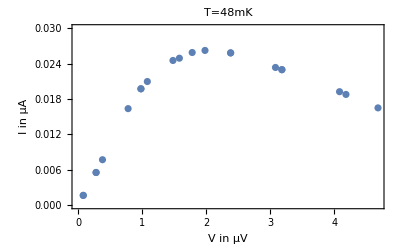
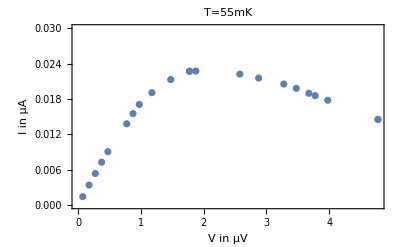
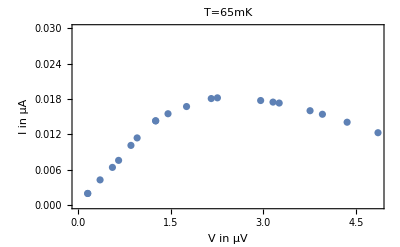
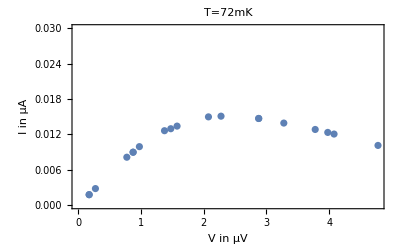

```mathematica
dir=NotebookDirectory[]<>"processed_data\\t_dependence\\";
idx={3,5,7,9,11,13,14};
temp=IntegerPart@(Identity@@@Import[dir<>"temp.csv"]);
xar={};yar={};
plotsd={};
For[ind=1, ind≤Length[idx], ind++,
path=dir<>ToString[idx[[ind]]-1];
Print[path<>"x.csv"];
x=Identity@@@Import[path<>"x.csv"];
y=Identity@@@Import[path<>"y.csv"];
xy=Transpose@{x,y};
xy=Select[xy,0<=#[[1]]≤vmax&];
x=N@Transpose[xy][[1]];
y=N@Transpose[xy][[2]];
AppendTo[xar, x]; AppendTo[yar, y];
AppendTo[plotsd,ListPlot[xy,PlotRange->{0,0.03},Frame->True,PlotLabel->"T="<>ToString[temp[[ind]]]<>"mK",FrameLabel->{Style["V in μV",s],Style["I in μA",s]}]];
]
plotsd
```

#### Define optimization function and minimize

```mathematica
(* define least square optimization function that fits all of above datasets at the same time. *)
mf[i0_?NumericQ,r1_?NumericQ,r2_?NumericQ]:=N[∑_(i=1)^Length[idx] (Norm[ yar[[i]] - fpoints[xar[[i]]+r2 yar[[i]], i0,r1, r2, 10^-3 temp[[idx[[i]]]] ] ]^2 ) ]
(*minimize and return fit parameters, i0 (μA), r1,r2 (Ω)*)
fp=FindMinimum[{mf[i0, r1, r2],i0>0.02,i0<0.04},{{i0,0.0348},{r1,58.6},{r2,88.4}},AccuracyGoal->3]
```

{0.000252192,{i0→0.0348167,r1→59.3078,r2→91.78}}

```mathematica
Plot fits
```

fits Plot

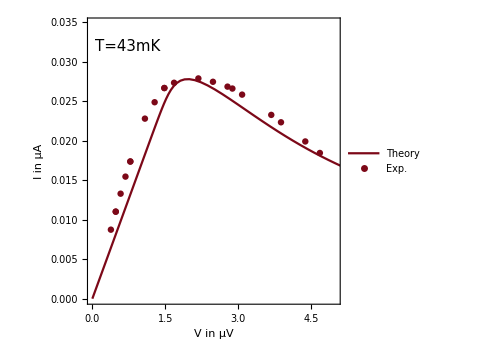
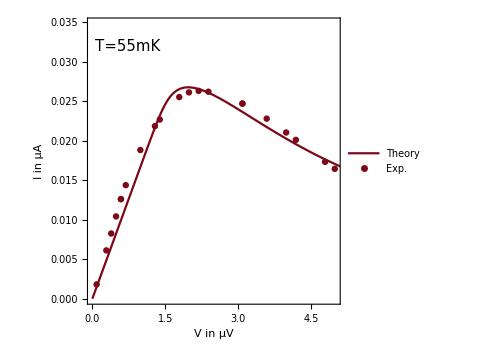
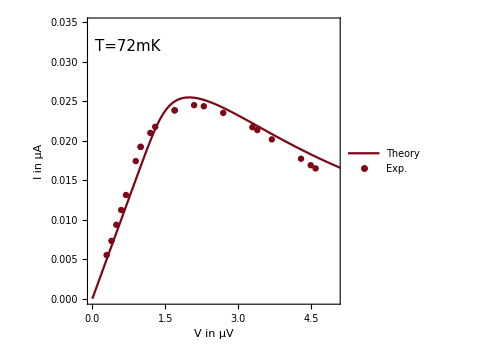
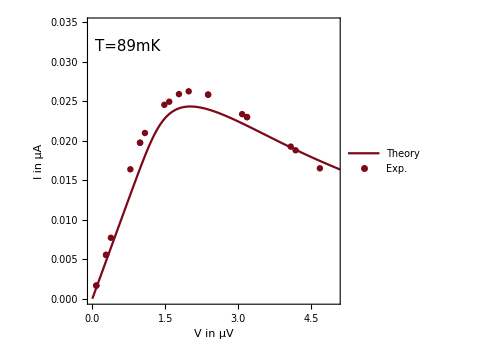
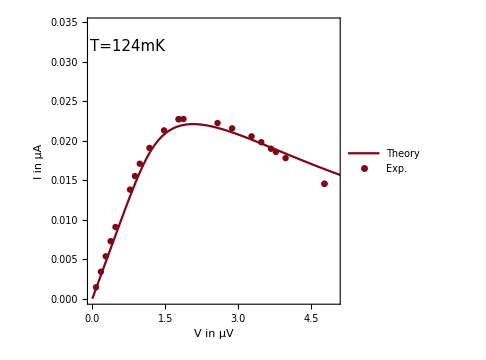
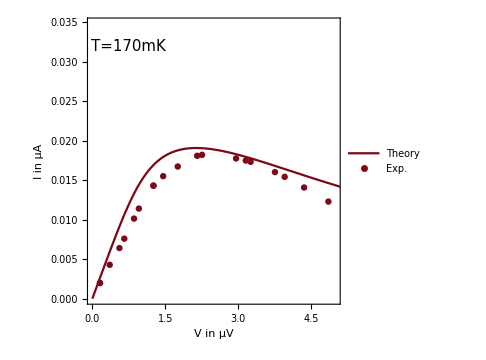
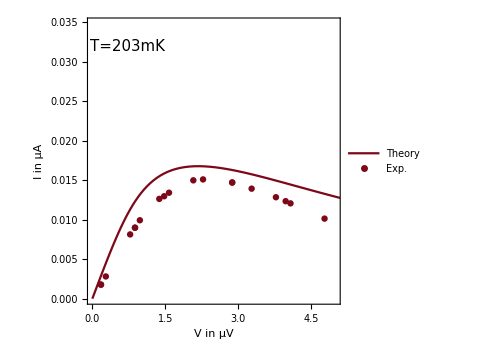

```mathematica
plots={};
For[sel=1, sel≤Length[idx], sel++,
T = temp[[idx[[sel]]  ]]10^-3;
xvals=linspace[0,vmax*2,100];
res=fpoints[xvals ,i0, r1,r2, T]/.fp[[2]];
vvals =xvals-r2*res/.fp[[2]];
xysel=Transpose@{xar[[sel]],N[yar[[sel]]]};
pl=Show[{
ListPlot[Transpose@{vvals,res},
PlotRange->{{0,vmax},{0,i0/.fp[[2]]}},Joined->True,Frame->True, FrameLabel->{Style["V in μV",s],Style["I in μA",s]},PlotLegends->Placed[{"Theory"},{Scaled[{0.85,0.9}],{0.5,0.5}}],
PlotStyle->ColorData[6,"ColorList"],
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],
ImageSize->Medium,
Epilog->{Text[Style["T="<>ToString[temp[[idx[[sel]]]]]<>"mK",s],Scaled[{0.16,0.9}]]}
],

ListPlot[xysel,PlotLegends->Placed[{"Exp."},{Scaled[{0.85,0.8}],{0.5,0.5}}],PlotStyle->ColorData[6,"ColorList"]]
}];
AppendTo[plots,pl];
]
plots
```

#### Save fits for all temperatures in folder “figures/fits”

```mathematica
folder=NotebookDirectory[]<>"figures\\fits\\";
Imaxfit={};
Imaxexp={};
For[i=1, i ≤Length[temp], i++,
x=Identity@@@Import[dir<>ToString[i-1]<>"x.csv"];
y=Identity@@@Import[dir<>ToString[i-1]<>"y.csv"];

xy=Transpose@{x,y};
xy=Select[xy,0<#[[1]]<=5&];
x=N@Transpose[xy][[1]];
y=N@Transpose[xy][[2]];

xysel=Transpose@{x,N[y*1000]};

T = temp[[i]] 10^-3;

xvals=linspace[0,vmax*2,100];
res=fpoints[xvals ,i0, r1,r2, T]/.fp[[2]];
vvals =xvals-r2*res/.fp[[2]];
AppendTo[Imaxfit, Max[res]];(*get maximum current of fit*)
AppendTo[Imaxexp, Max [N[y]]];(*get maximum current of experimental data*)
Export[folder<>"res"<>ToString[i-1]<>".pdf",

Show[{
ListPlot[Transpose@{vvals,res*1000},
PlotRange->{{0,vmax},{0,i0*1000/.fp[[2]]}},Joined->True,Frame->True, FrameLabel->{Style["V in μV",s],Style["I in nA",s]},PlotLegends->Placed[{"Theory"},{Scaled[{0.85,0.9}],{0.5,0.5}}],
PlotStyle->ColorData[6,"ColorList"],
AspectRatio->1,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],
ImageSize->Medium,
Epilog->{Text[Style["T="<>ToString[T 10^3]<>"mK",s],Scaled[{0.16,0.9}]]}
],

ListPlot[xysel,PlotLegends->Placed[{"Exp."},{Scaled[{0.85,0.8}],{0.5,0.5}}],PlotStyle->ColorData[6,"ColorList"]]
}]

]
]
```

```mathematica
Plot and save maximum current vs. temperature
```

and current maximum Plot save vs.temperature

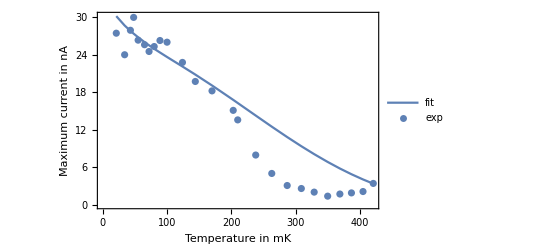

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\figures\fits\..//figure_3_f.pdf

```mathematica
mc=Show[{ListPlot[Transpose@{temp,Imaxfit*1000},Joined->True,Frame->True,FrameLabel->{"Temperature in mK","Maximum current in nA"},PlotLegends->{"fit"}],
ListPlot[Transpose@{temp,Imaxexp*1000},Joined->False,PlotLegends->{"exp"}]},LabelStyle->Directive[FontSize->15,Bold]]
Export[folder<>"..//figure_3_f.pdf",mc]
```

#### Fraunhofer Pattern

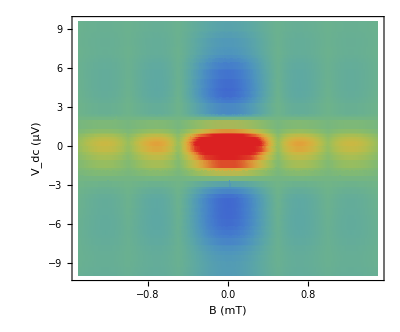

C:\Users\rafae\Desktop\ZBCP LJ16617 Yu\fig_3_temperature_dependence\figures\fits\..//figure_4_c.pdf

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
bfolder=NotebookDirectory[]<>"//processed_data//b_dependence";
data=Import[bfolder<>"//data.txt","Table"];
bval=Import[bfolder<>"//bval.txt","Table"];
vval=Import[bfolder<>"//V.txt","Table"];

xval=Flatten@Import[bfolder<>"//x.txt","Table"];
yval=Flatten@Import[bfolder<>"//y.txt","Table"];
pl=ArrayFlatten[Transpose[{bval, vval,data},{3,2,1}],1];

bdep=ListDensityPlot[pl,ColorFunction->(ColorData["Rainbow"][Rescale[#,{1.35,3}]]&),PlotRange->All,
Axes->False,ColorFunctionScaling->False,
FrameLabel->{Style["B (mT)",s],Style["V_dc (μV)",s]},
AspectRatio->0.83,
FrameTicksStyle->Directive[s],
FrameStyle->Thickness[0.002],PlotLegends->Automatic,LabelStyle->Directive[15]]
Export[folder<>"..//figure_4_c.pdf",bdep]
```